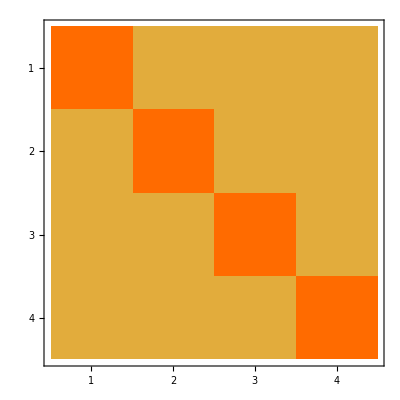
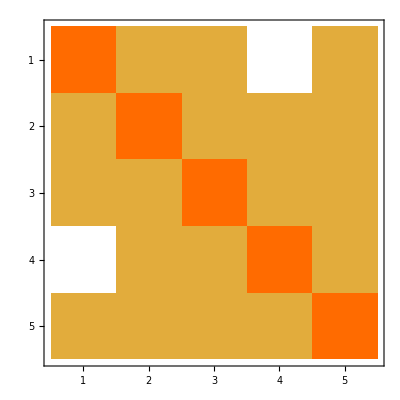
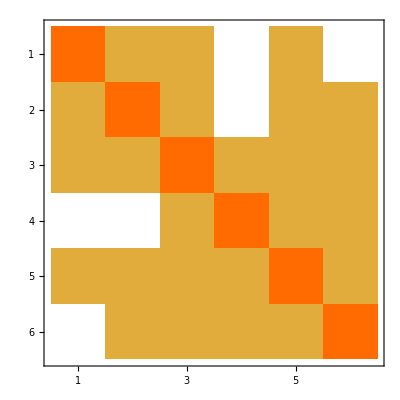
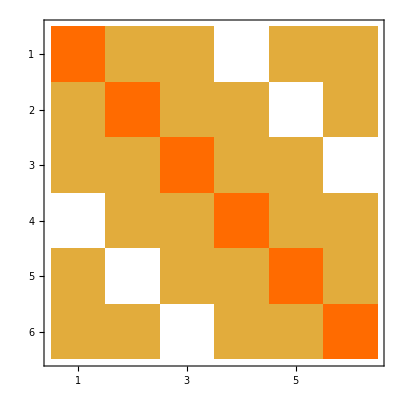
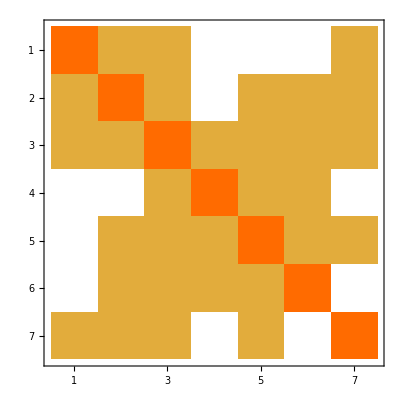
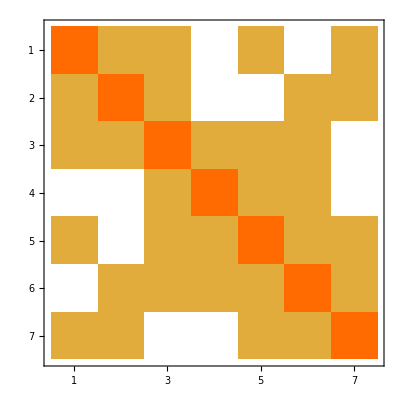
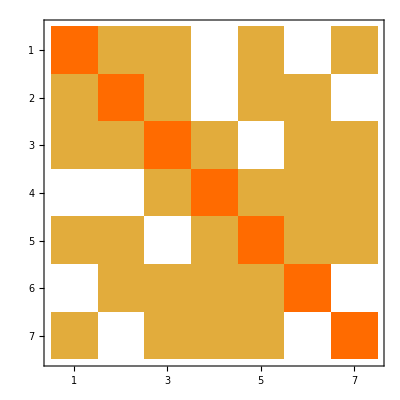
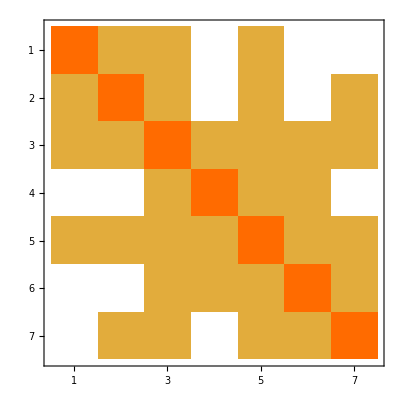
{{-Graphics-,{v1x2x3x4}},{-Graphics-,{v14x2x3x5}},{-Graphics-,{v16x24x3x5}},{-Graphics-,{v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x25x36}},{-Graphics-,{v15x24x3x67}},{-Graphics-,{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4}},{-Graphics-,{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4}},{-Graphics-,{v147x26x3x5}},{-Graphics-,{v16x24x3x57}},{-Graphics-,{v15x28x34x67}},{-Graphics-,{v18x24x35x67,v14x28x35x67,v168x2x35x47,v16x28x35x47,v168x24x35x7}},{-Graphics-,{v145x28x3x67}},{-Graphics-,{v15x26x3x478}},{-Graphics-,{v158x2x36x47,v158x24x3x67,v158x24x36x7,v15x24x36x78}},{-Graphics-,{v15x24x38x67,v14x25x38x67,v148x25x3x67,v16x25x38x47}},{-Graphics-,{v158x24x3x67}},{-Graphics-,{v15x24x38x67}},{-Graphics-,{v14x28x35x67,v16x28x35x47,v15x24x37x68}},{-Graphics-,{v14x28x35x67,v18x24x35x67,v16x28x35x47,v15x28x34x67}},{-Graphics-,{v14x25x37x68,v16x248x37x5,v16x25x3x478,v16x25x37x48}},{-Graphics-,{v1x267x35x48,v16x24x35x78,v16x27x35x48,v14x26x35x78,v14x267x35x8,v148x2x35x67,v148x26x35x7,v18x24x35x67,v148x267x3x5,v18x267x35x4,v148x27x35x6,v148x267x35}},{-Graphics-,{v178x246x3x5}},{-Graphics-,{v16x24x38x57}},{-Graphics-,{v15x26x34x789}},{-Graphics-,{v159x24x36x78,v159x28x34x67,v159x28x36x47,v15x28x36x479}},{-Graphics-,{v156x2x34x789,v156x24x3x789,v156x24x39x78,v156x28x34x79,v156x28x39x47}},{-Graphics-,{v145x28x39x67}},{-Graphics-,{v15x28x39x467}},{-Graphics-,{v167x28x34x59}},{-Graphics-,{v16x278x349x5,v15x28x349x67,v15x278x34x69,v15x278x349x6}},{-Graphics-,{v149x28x35x67,v18x249x35x67,v169x24x35x78,v16x249x35x78,v169x28x35x47}},{-Graphics-,{v159x28x34x67}},{-Graphics-,{v15x28x349x67}},{-Graphics-,{v15x289x34x67}},{-Graphics-,{v156x24x39x78,v156x28x34x79,v156x28x39x47,v145x28x39x67}},{-Graphics-,{v189x25x34x67,v156x24x39x78,v156x28x39x47}},{-Graphics-,{v1x268x35x479,v18x26x35x479,v168x2x35x479,v16x28x35x479,v168x24x35x79,v14x268x35x79,v149x28x35x67,v149x268x35x7,v19x268x35x47,v189x26x35x47,v189x24x35x67,v15x268x3x479}},{-Graphics-,{v189x24x35x67,v168x24x35x79,v159x28x36x47}},{-Graphics-,{v147x2x35x689,v147x28x35x69,v17x24x35x689,v167x28x35x49,v167x24x35x89}},{-Graphics-,{v1x247x35x689,v18x247x35x69,v14x27x35x689,v168x247x35x9,v16x247x35x89,v168x27x35x49,v168x247x39x5,v15x247x3x689,v15x247x39x68}}}

```mathematica
Table[{MatrixFromGraph[ReadGrof[k]]//MatrixPlot,FindFullFormula1234[ReadGrof[k]]},{k,1,40}]
```

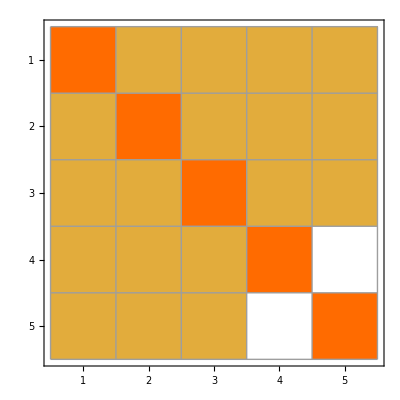

```mathematica
Block[{m=MatrixFromGraph[MinimalGraph[4]]},
m[[All,{3,4}]]=m[[All,{4,3}]];
m[[{3,4}]]=m[[{4,3}]];
MatrixPlot[ m,Mesh->All]]
```

```mathematica
Swap[m_,i_,j_]:=Block[{c=m},

c[[All,{i,j}]]=c[[All,{j,i}]];
c[[{i,j}]]=c[[{j,i}]];
c
]
```

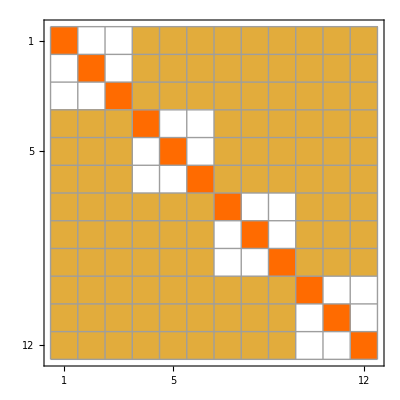
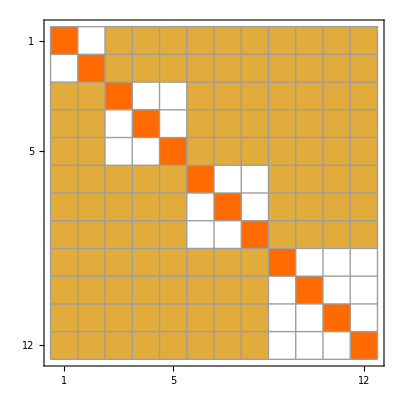
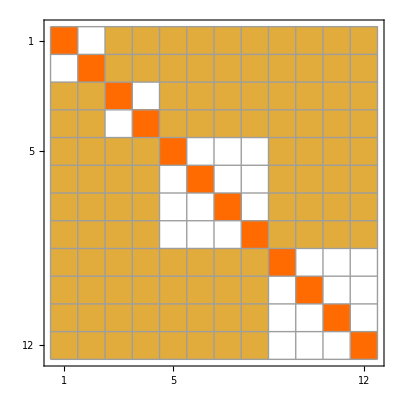
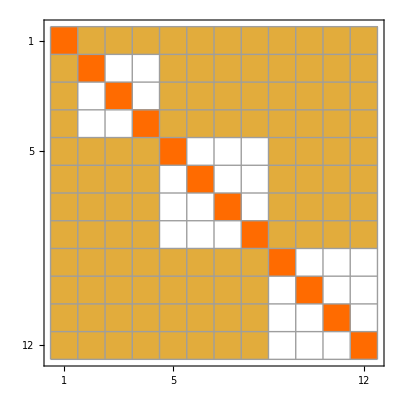
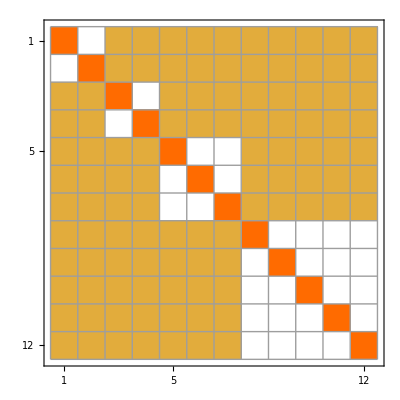
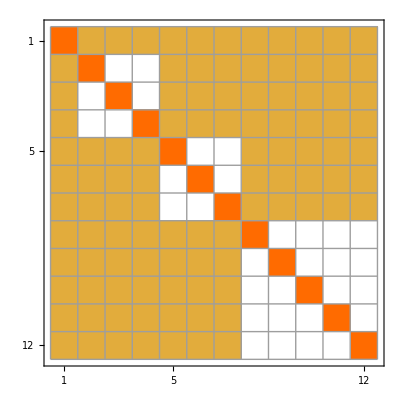
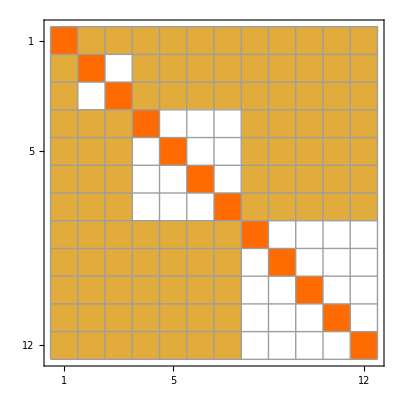
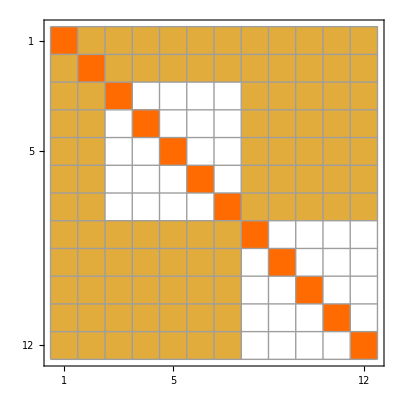

```mathematica
Map[With[{g=#},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
MatrixPlot[ m,Mesh->All]]]&,BarelyFourColorableGraphsOfCount[12]]//Sort
```

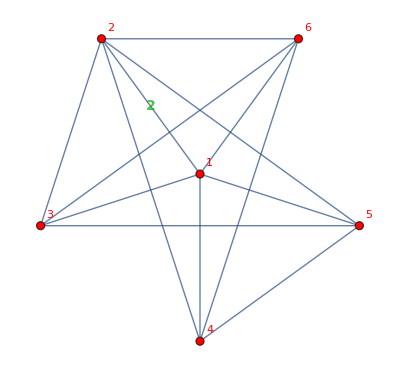
```mathematica
Block[{m,size=6},
m=MatrixFromGraph[-Graphics-];
size=6;
MatrixPlot[ m,Mesh->All]]
```

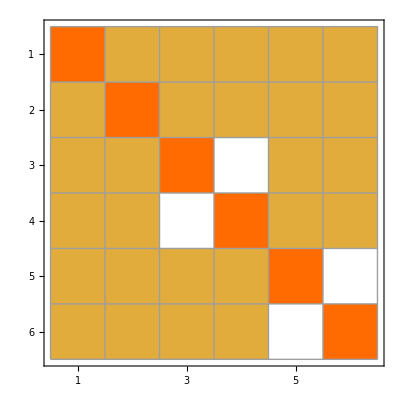

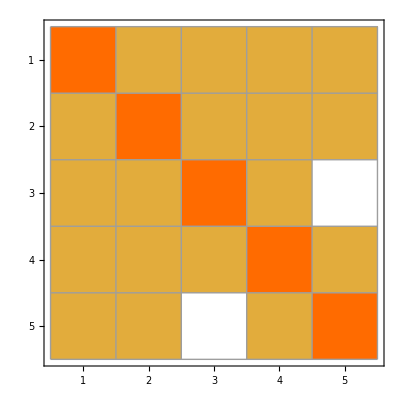
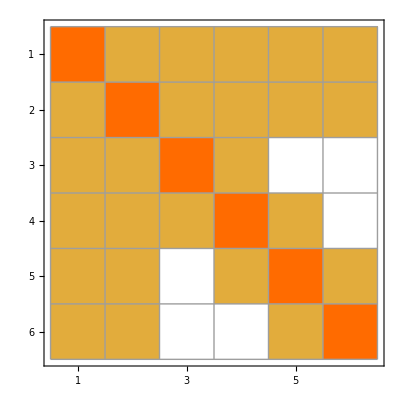
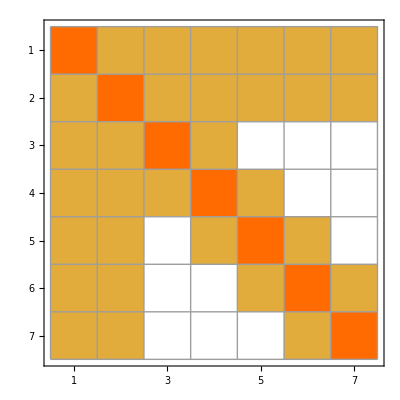
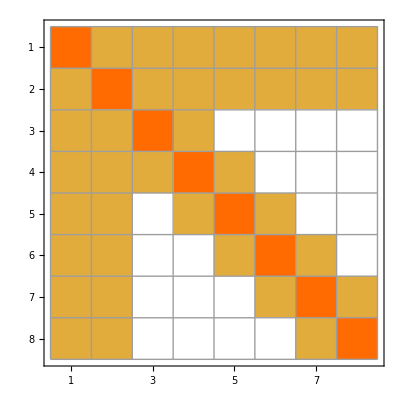
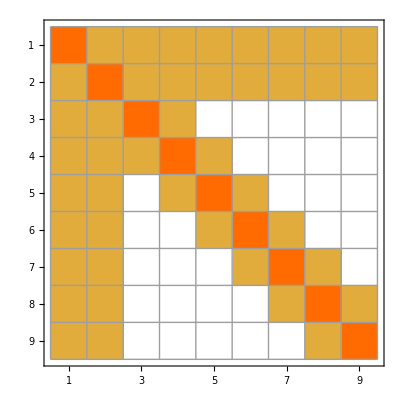
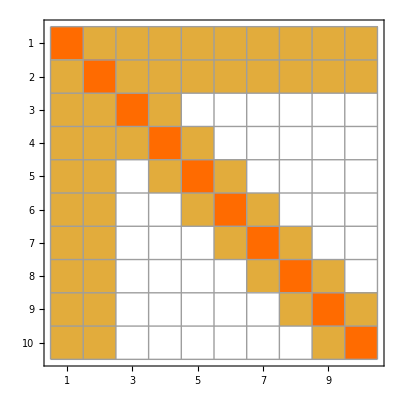
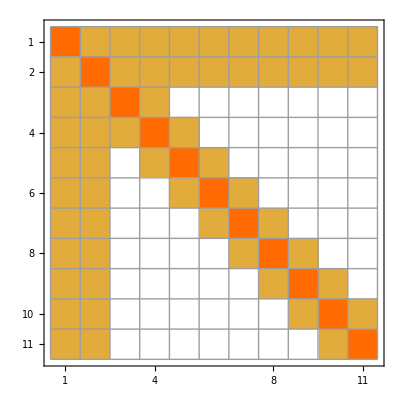
{{-Graphics-,{v1x2x35x4}},{-Graphics-,{v1x2x35x46}},{-Graphics-,{v1x2x357x46}},{-Graphics-,{v1x2x357x468}},{-Graphics-,{v1x2x3579x468}},{-Graphics-,{v1x2x3579x468a}},{-Graphics-,{v1x2x3579bx468a}},{-Graphics-,{v1x2x3579bx468ac}},{-Graphics-,{v1x2x3579bdx468ac}},{-Graphics-,{v1x2x3579bdx468ace}},{-Graphics-,{v1x2x3579bdfx468ace}},{-Graphics-,{v1x2x3579bdfx468aceg}},{-Graphics-,{v1x2x3579bdfhx468aceg}},{-Graphics-,{v1x2x3579bdfhx468acegi}},{-Graphics-,{v1x2x3579bdfhjx468acegi}},{-Graphics-,{v1x2x3579bdfhjx468acegik}},{-Graphics-,{v1x2x3579bdfhjlx468acegik}}}

```mathematica
Table[With[{g=MinimalGraph[k]},{MatrixPlot[ MatrixFromGraph[g],Mesh->All],FindFullFormula1234[g]}],{k,4,20}]
```

First::nofirst: {} has zero length and no first element.

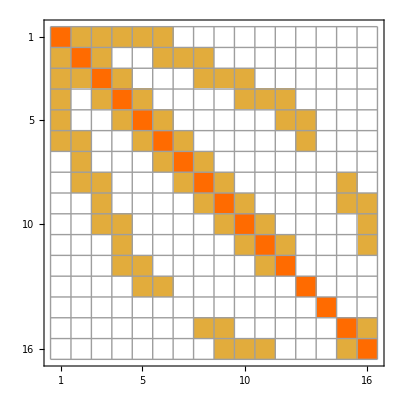
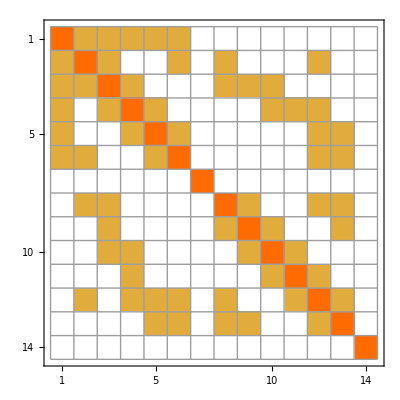
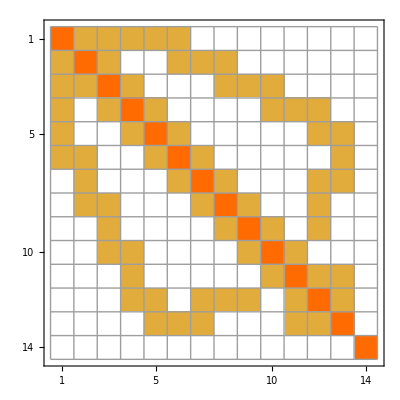
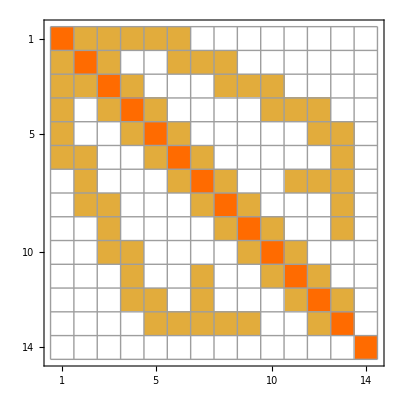
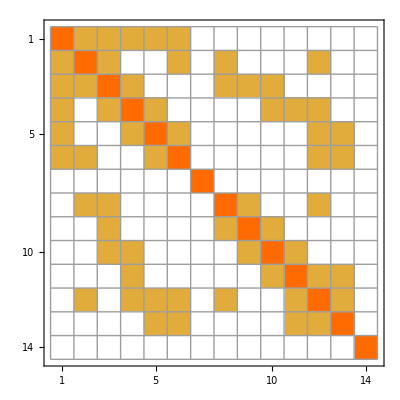
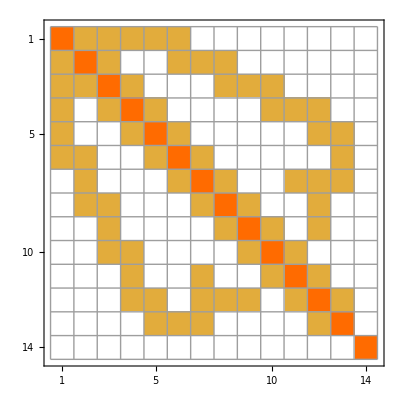
{{-Graphics-,v1gx249dx357bfx68ach},{-Graphics-,v1adx259bx3cgx468h},{-Graphics-,v1acx29dx357bx468g},{-Graphics-,First[{}]},{-Graphics-,v1cgx249dx36bfx58a},{-Graphics-,v1acx29bdx357x468g}}

```mathematica
Table[With[{g=EmbedGraphInPlantri8[allGraphs5,k]},{MatrixPlot[MatrixFromGraph[g],Mesh->All],First[FindFullFormula1234[g]]}],{k,Prepend[alfa1s,0]}]
```

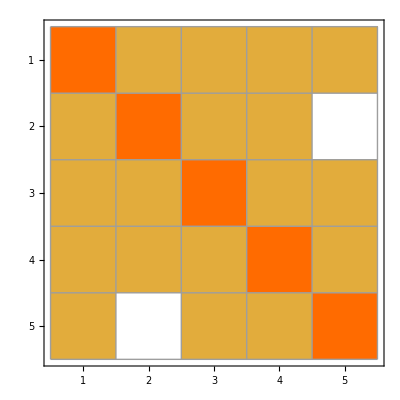
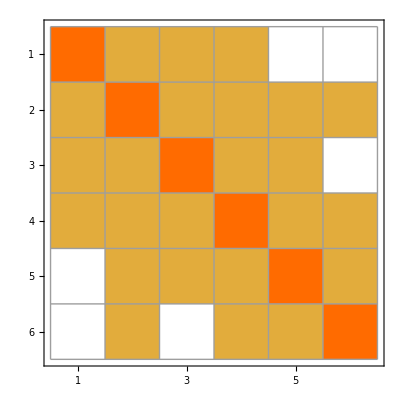
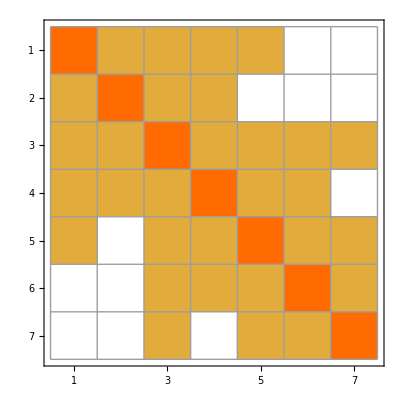
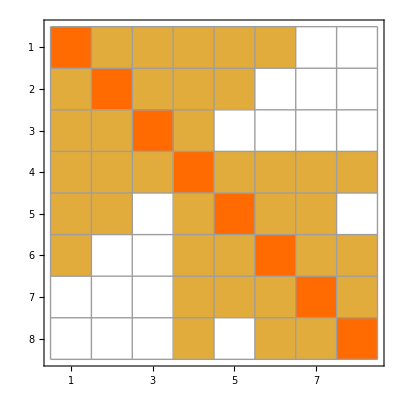
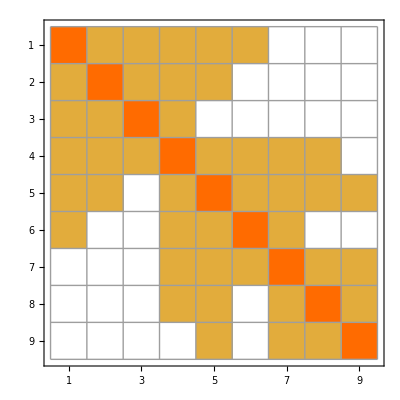
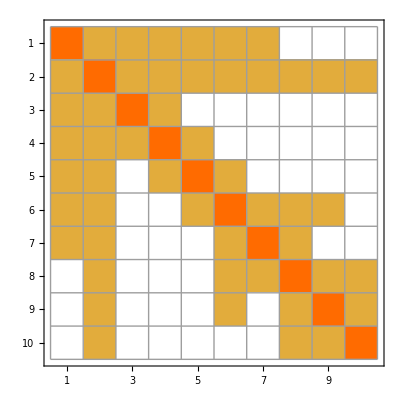
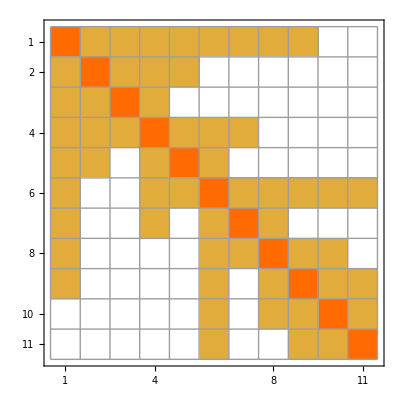
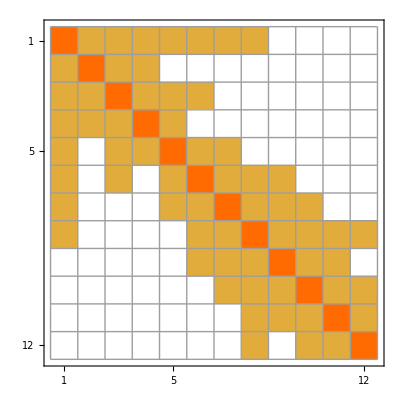
{{-Graphics-,{v1x25x3x4}},{-Graphics-,{v15x2x36x4}},{-Graphics-,{v16x25x3x47}},{-Graphics-,{v17x26x358x4}},{-Graphics-,{v17x268x35x49}},{-Graphics-,{v18x2x3579x46a}},{-Graphics-,{v1ax26x3579x48b}},{-Graphics-,{v19cx258x37bx46a}},{-Graphics-,{v18adx2579x3bx46c}},{-Graphics-,{v1579cx26ax3bdx48e}},{-Graphics-,{v18cex25ax36bdfx479}},{-Graphics-,{v1cex258afx36x479bdg}},{-Graphics-,{v157dfhx29egx36acx48b}},{-Graphics-,{v169fx27cix358aehx4bdg}},{-Graphics-,{v1gx27bdfix358acx469ehj}},{-Graphics-,{v157bfx2achjx38dgx469eik}},{-Graphics-,{v1chkx268adfx35jx479begil}}}

```mathematica
Table[With[{g=MinimalGraph2[k]},{MatrixPlot[MatrixFromGraph[g],Mesh->All],FindFullFormula1234[g]}],{k,4,20}]
```

```mathematica
ChromaticPolynomial[ReadGrof[3],3]
```

0

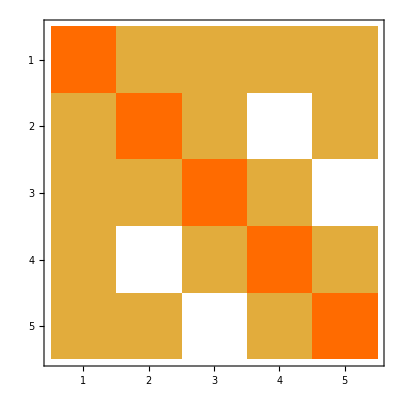
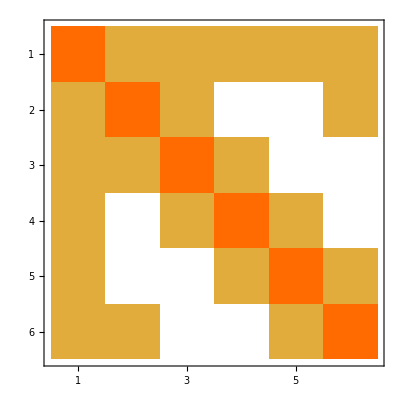
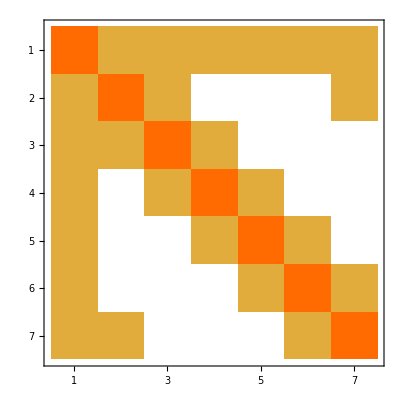
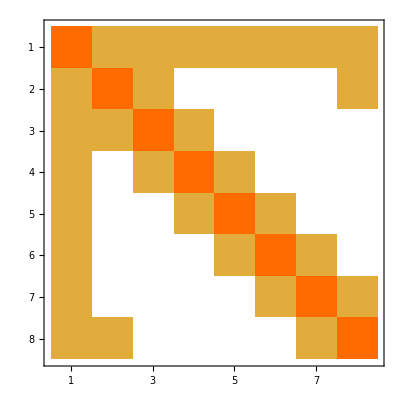
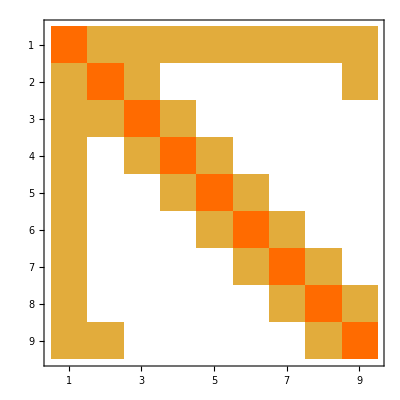
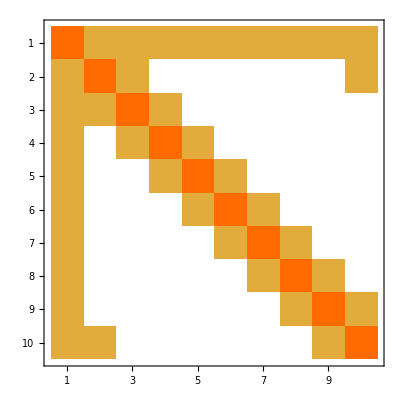
{{-Graphics-,{v1x2x3x4}},{-Graphics-,{v1x2x35x4,v1x24x3x5,v1x24x35}},{-Graphics-,{v1x2x35x46,v1x25x3x46,v1x25x36x4,v1x24x36x5,v1x24x35x6}},{-Graphics-,{v1x2x357x46,v1x26x357x4,v1x26x35x47,v1x25x37x46,v1x25x36x47,v1x246x3x57,v1x246x37x5,v1x24x36x57,v1x24x357x6,v1x246x35x7,v1x246x357}},{-Graphics-,{v1x2x357x468,v1x27x35x468,v1x27x358x46,v1x26x357x48,v1x26x358x47,v1x257x3x468,v1x257x38x46,v1x25x37x468,v1x257x368x4,v1x257x36x48,v1x25x368x47,v1x246x38x57,v1x246x37x58,v1x247x368x5,v1x247x36x58,v1x24x368x57,v1x247x358x6,v1x246x358x7,v1x246x357x8,v1x24x357x68,v1x247x35x68}},{-Graphics-,{v1x2x3579x468,v1x28x357x469,v1x28x3579x46,v1x27x359x468,v1x27x358x469,v1x268x3579x4,v1x268x357x49,v1x26x3579x48,v1x26x358x479,v1x268x35x479,v1x268x359x47,v1x257x39x468,v1x257x38x469,v1x25x379x468,v1x258x37x469,v1x258x379x46,v1x257x368x49,v1x257x369x48,v1x25x368x479,v1x258x36x479,v1x258x369x47,v1x2468x3x579,v1x2468x39x57,v1x246x38x579,v1x2468x379x5,v1x2468x37x59,v1x246x379x58,v1x247x368x59,v1x247x369x58,v1x24x368x579,v1x248x36x579,v1x248x369x57,v1x248x3579x6,v1x246x3579x8,v1x246x358x79,v1x248x357x69,v1x247x358x69,v1x2468x359x7,v1x2468x357x9,v1x247x359x68,v1x24x3579x68,v1x2468x35x79,v1x2468x3579}},{-Graphics-,{v1x2x3579x468a,v1x29x357x468a,v1x29x357ax468,v1x28x357ax469,v1x28x3579x46a,v1x279x35ax468,v1x279x358x46a,v1x27x358ax469,v1x27x359x468a,v1x279x35x468a,v1x279x358ax46,v1x268x3579x4a,v1x268x357ax49,v1x269x357x48a,v1x269x357ax48,v1x26x3579x48a,v1x269x358x47a,v1x268x35ax479,v1x268x359x47a,v1x26x358ax479,v1x269x358ax47,v1x2579x3x468a,v1x2579x3ax468,v1x257x39x468a,v1x257x38ax469,v1x2579x38x46a,v1x2579x38ax46,v1x259x37ax468,v1x258x37ax469,v1x258x379x46a,v1x25x379x468a,v1x259x37x468a,v1x2579x368ax4,v1x2579x368x4a,v1x257x368ax49,v1x257x369x48a,v1x2579x36x48a,v1x2579x36ax48,v1x259x368x47a,v1x258x36ax479,v1x258x369x47a,v1x25x368ax479,v1x259x368ax47,v1x2468x3ax579,v1x2468x39x57a,v1x246x38ax579,v1x2469x38x57a,v1x2469x38ax57,v1x2468x379x5a,v1x2468x37ax59,v1x246x379x58a,v1x2469x37x58a,v1x2469x37ax58,v1x2479x368ax5,v1x2479x368x5a,v1x247x368ax59,v1x247x369x58a,v1x2479x36x58a,v1x2479x36ax58,v1x249x368x57a,v1x248x36ax579,v1x248x369x57a,v1x24x368ax579,v1x249x368ax57,v1x2479x358ax6,v1x246x358ax79,v1x246x3579x8a,v1x2479x358x6a,v1x248x3579x6a,v1x2469x358ax7,v1x2469x357x8a,v1x247x358ax69,v1x2469x357ax8,v1x2469x358x7a,v1x248x357ax69,v1x249x357x68a,v1x247x359x68a,v1x2468x357ax9,v1x2468x359x7a,v1x249x357ax68,v1x2468x3579xa,v1x24x3579x68a,v1x2479x35x68a,v1x2479x35ax68,v1x2468x35ax79}}}

```mathematica
Table[With[{g=WheelGraph[k]},{MatrixFromGraph[g]//MatrixPlot,FindFullFormula1234[g]}],{k,4,10}]
```

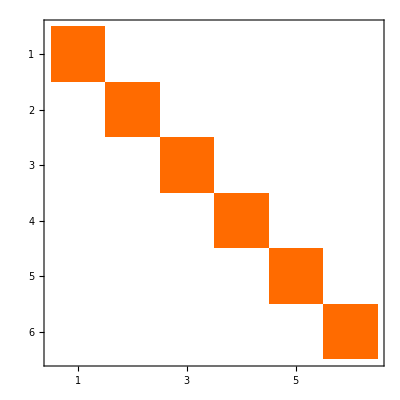
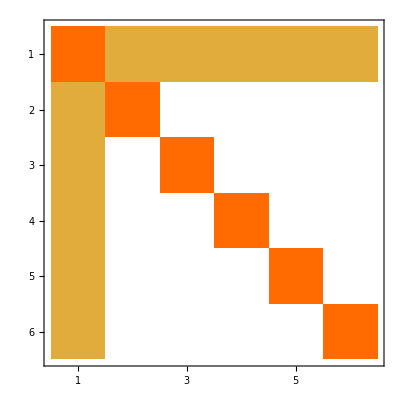
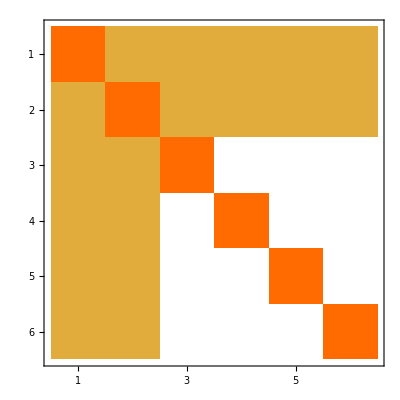
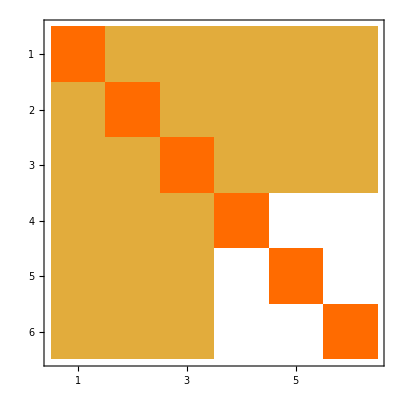
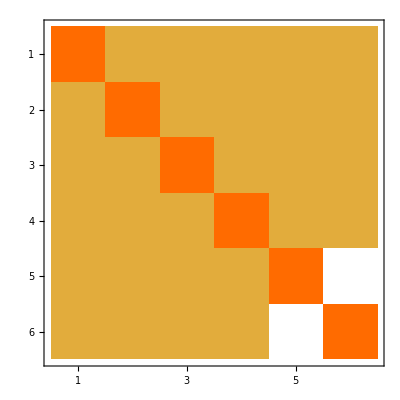
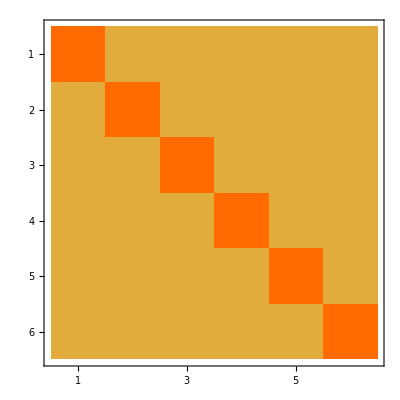
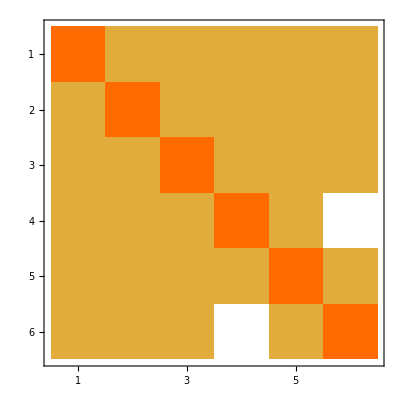
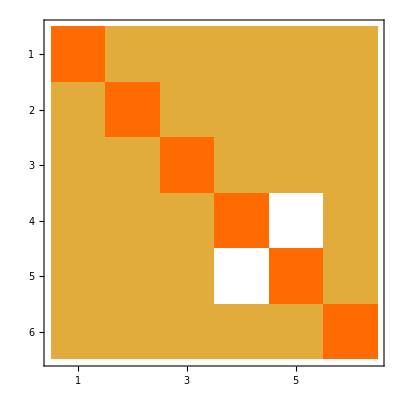
{{-Graphics-,{v1x2x3x456,v1x2x36x45,v1x2x356x4,v1x2x35x46,v1x2x346x5,v1x2x345x6,v1x2x34x56,v1x2x3456,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v1x256x3x4,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v1x256x34,v1x246x3x5,v1x245x3x6,v1x24x3x56,v1x2456x3,v1x24x36x5,v1x245x36,v1x24x35x6,v1x24x356,v1x246x35,v1x236x4x5,v1x235x4x6,v1x23x4x56,v1x2356x4,v1x234x5x6,v1x234x56,v1x23x46x5,v1x2346x5,v1x235x46,v1x23x45x6,v1x2345x6,v1x23x456,v1x236x45,v1x23456,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345,v16x25x3x4,v16x25x34,v16x24x3x5,v16x245x3,v16x24x35,v16x23x4x5,v16x235x4,v16x234x5,v16x23x45,v16x2345,v156x2x3x4,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346,v156x2x34,v15x26x3x4,v15x26x34,v15x24x3x6,v15x246x3,v156x24x3,v15x24x36,v15x23x4x6,v15x236x4,v156x23x4,v15x234x6,v156x234,v15x23x46,v15x2346,v146x2x3x5,v145x2x3x6,v14x2x3x56,v1456x2x3,v14x2x36x5,v145x2x36,v14x2x35x6,v14x2x356,v146x2x35,v14x26x3x5,v145x26x3,v14x26x35,v14x25x3x6,v14x256x3,v146x25x3,v14x25x36,v14x23x5x6,v14x236x5,v146x23x5,v14x235x6,v146x235,v145x23x6,v145x236,v14x23x56,v14x2356,v1456x23,v136x2x4x5,v135x2x4x6,v13x2x4x56,v1356x2x4,v134x2x5x6,v134x2x56,v13x2x46x5,v1346x2x5,v135x2x46,v13x2x45x6,v1345x2x6,v13x2x456,v136x2x45,v13456x2,v13x26x4x5,v135x26x4,v134x26x5,v13x26x45,v1345x26,v13x25x4x6,v13x256x4,v136x25x4,v134x25x6,v134x256,v13x25x46,v1346x25,v13x24x5x6,v13x246x5,v136x24x5,v13x245x6,v136x245,v135x24x6,v135x246,v13x24x56,v13x2456,v1356x24,v126x3x4x5,v125x3x4x6,v12x3x4x56,v1256x3x4,v124x3x5x6,v124x3x56,v12x3x46x5,v1246x3x5,v125x3x46,v12x3x45x6,v1245x3x6,v12x3x456,v126x3x45,v12456x3,v123x4x5x6,v123x4x56,v123x46x5,v123x45x6,v123x456,v12x36x4x5,v1236x4x5,v125x36x4,v124x36x5,v12x36x45,v1245x36,v1236x45,v12x35x4x6,v1235x4x6,v12x356x4,v126x35x4,v12356x4,v124x35x6,v124x356,v12x35x46,v1246x35,v1235x46,v12x34x5x6,v1234x5x6,v12x346x5,v126x34x5,v12346x5,v12x345x6,v126x345,v125x34x6,v12345x6,v125x346,v12x34x56,v12x3456,v1256x34,v1234x56,v123456}},{-Graphics-,{v1x2x3x456,v1x2x36x45,v1x2x356x4,v1x2x35x46,v1x2x346x5,v1x2x345x6,v1x2x34x56,v1x2x3456,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v1x256x3x4,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v1x256x34,v1x246x3x5,v1x245x3x6,v1x24x3x56,v1x2456x3,v1x24x36x5,v1x245x36,v1x24x35x6,v1x24x356,v1x246x35,v1x236x4x5,v1x235x4x6,v1x23x4x56,v1x2356x4,v1x234x5x6,v1x234x56,v1x23x46x5,v1x2346x5,v1x235x46,v1x23x45x6,v1x2345x6,v1x23x456,v1x236x45,v1x23456}},{-Graphics-,{v1x2x3x456,v1x2x36x45,v1x2x356x4,v1x2x35x46,v1x2x346x5,v1x2x345x6,v1x2x34x56,v1x2x3456}},{-Graphics-,{v1x2x3x456}},{-Graphics-,{}},{-Graphics-,{}},{-Graphics-,{}},{-Graphics-,{}},{-Graphics-,{}},{-Graphics-,{v1x2x36x45}},{-Graphics-,{}},{-Graphics-,{v1x2x35x46}},{-Graphics-,{v1x2x356x4}},{-Graphics-,{v1x2x34x56}},{-Graphics-,{}},{-Graphics-,{v1x2x346x5}},{-Graphics-,{v1x2x345x6}},{-Graphics-,{}},{-Graphics-,{v1x26x3x45}},{-Graphics-,{v1x26x35x4}},{-Graphics-,{v1x26x34x5}},{-Graphics-,{v1x2x345x6,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345}},{-Graphics-,{}},{-Graphics-,{v1x25x3x46}},{-Graphics-,{v1x25x36x4}},{-Graphics-,{v1x25x34x6}},{-Graphics-,{v1x2x346x5,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346}},{-Graphics-,{v1x256x3x4}},{-Graphics-,{v1x2x34x56,v1x26x34x5,v1x256x3x4,v1x25x34x6,v1x256x34}},{-Graphics-,{v1x24x3x56}},{-Graphics-,{}},{-Graphics-,{v1x24x36x5}},{-Graphics-,{v1x24x35x6}},{-Graphics-,{v1x2x356x4,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x24x356}},{-Graphics-,{v1x246x3x5}},{-Graphics-,{v1x2x35x46,v1x26x35x4,v1x246x3x5,v1x24x35x6,v1x246x35}},{-Graphics-,{v1x245x3x6}},{-Graphics-,{v1x2x36x45,v1x25x36x4,v1x245x3x6,v1x24x36x5,v1x245x36}},{-Graphics-,{v1x2x3x456,v1x26x3x45,v1x256x3x4,v1x25x3x46,v1x246x3x5,v1x245x3x6,v1x24x3x56,v1x2456x3}},{-Graphics-,{v1x2x3x456,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x456}},{-Graphics-,{v1x23x4x56}},{-Graphics-,{}},{-Graphics-,{v1x23x46x5}},{-Graphics-,{v1x23x45x6}},{-Graphics-,{v1x236x4x5}},{-Graphics-,{v1x2x36x45,v1x26x3x45,v1x236x4x5,v1x23x45x6,v1x236x45}},{-Graphics-,{v1x235x4x6}},{-Graphics-,{v1x2x35x46,v1x25x3x46,v1x235x4x6,v1x23x46x5,v1x235x46}},{-Graphics-,{v1x2x356x4,v1x26x35x4,v1x256x3x4,v1x25x36x4,v1x236x4x5,v1x235x4x6,v1x23x4x56,v1x2356x4}},{-Graphics-,{v1x2x34x56,v1x24x3x56,v1x23x4x56,v1x234x5x6,v1x234x56}},{-Graphics-,{v1x234x5x6}},{-Graphics-,{v1x2x346x5,v1x26x34x5,v1x246x3x5,v1x24x36x5,v1x236x4x5,v1x234x5x6,v1x23x46x5,v1x2346x5}},{-Graphics-,{v1x2x345x6,v1x25x34x6,v1x245x3x6,v1x24x35x6,v1x235x4x6,v1x234x5x6,v1x23x45x6,v1x2345x6}},{-Graphics-,{}},{-Graphics-,{v16x2x3x45}},{-Graphics-,{v16x2x35x4}},{-Graphics-,{v16x2x34x5}},{-Graphics-,{v1x2x345x6,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345}},{-Graphics-,{v16x25x3x4}},{-Graphics-,{v1x25x34x6,v16x2x34x5,v16x25x3x4,v16x25x34}},{-Graphics-,{v16x24x3x5}},{-Graphics-,{v1x24x35x6,v16x2x35x4,v16x24x3x5,v16x24x35}},{-Graphics-,{v1x245x3x6,v16x2x3x45,v16x25x3x4,v16x24x3x5,v16x245x3}},{-Graphics-,{v16x23x4x5}},{-Graphics-,{v1x23x45x6,v16x2x3x45,v16x23x4x5,v16x23x45}},{-Graphics-,{v1x235x4x6,v16x2x35x4,v16x25x3x4,v16x23x4x5,v16x235x4}},{-Graphics-,{v1x234x5x6,v16x2x34x5,v16x24x3x5,v16x23x4x5,v16x234x5}},{-Graphics-,{v1x2x345x6,v1x25x34x6,v1x245x3x6,v1x24x35x6,v1x235x4x6,v1x234x5x6,v1x23x45x6,v1x2345x6,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345,v16x25x3x4,v16x25x34,v16x24x3x5,v16x245x3,v16x24x35,v16x23x4x5,v16x235x4,v16x234x5,v16x23x45,v16x2345}},{-Graphics-,{}},{-Graphics-,{v15x2x3x46}},{-Graphics-,{v15x2x36x4}},{-Graphics-,{v15x2x34x6}},{-Graphics-,{v1x2x346x5,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346}},{-Graphics-,{v15x26x3x4}},{-Graphics-,{v1x26x34x5,v15x2x34x6,v15x26x3x4,v15x26x34}},{-Graphics-,{v15x24x3x6}},{-Graphics-,{v1x24x36x5,v15x2x36x4,v15x24x3x6,v15x24x36}},{-Graphics-,{v1x246x3x5,v15x2x3x46,v15x26x3x4,v15x24x3x6,v15x246x3}},{-Graphics-,{v15x23x4x6}},{-Graphics-,{v1x23x46x5,v15x2x3x46,v15x23x4x6,v15x23x46}},{-Graphics-,{v1x236x4x5,v15x2x36x4,v15x26x3x4,v15x23x4x6,v15x236x4}},{-Graphics-,{v1x234x5x6,v15x2x34x6,v15x24x3x6,v15x23x4x6,v15x234x6}},{-Graphics-,{v1x2x346x5,v1x26x34x5,v1x246x3x5,v1x24x36x5,v1x236x4x5,v1x234x5x6,v1x23x46x5,v1x2346x5,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346,v15x26x3x4,v15x26x34,v15x24x3x6,v15x246x3,v15x24x36,v15x23x4x6,v15x236x4,v15x234x6,v15x23x46,v15x2346}},{-Graphics-,{v156x2x3x4}},{-Graphics-,{v1x2x34x56,v16x2x34x5,v156x2x3x4,v15x2x34x6,v156x2x34}},{-Graphics-,{v1x24x3x56,v16x24x3x5,v156x2x3x4,v15x24x3x6,v156x24x3}},{-Graphics-,{v1x23x4x56,v16x23x4x5,v156x2x3x4,v15x23x4x6,v156x23x4}},{-Graphics-,{v1x2x34x56,v1x24x3x56,v1x23x4x56,v1x234x5x6,v1x234x56,v16x2x34x5,v16x24x3x5,v16x23x4x5,v16x234x5,v156x2x3x4,v15x2x34x6,v156x2x34,v15x24x3x6,v156x24x3,v15x23x4x6,v156x23x4,v15x234x6,v156x234}},{-Graphics-,{v14x2x3x56}},{-Graphics-,{}},{-Graphics-,{v14x2x36x5}},{-Graphics-,{v14x2x35x6}},{-Graphics-,{v1x2x356x4,v14x2x3x56,v14x2x36x5,v14x2x35x6,v14x2x356}},{-Graphics-,{v14x26x3x5}},{-Graphics-,{v1x26x35x4,v14x2x35x6,v14x26x3x5,v14x26x35}},{-Graphics-,{v14x25x3x6}},{-Graphics-,{v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x25x36}},{-Graphics-,{v1x256x3x4,v14x2x3x56,v14x26x3x5,v14x25x3x6,v14x256x3}},{-Graphics-,{v1x23x4x56,v14x2x3x56,v14x23x5x6,v14x23x56}},{-Graphics-,{v14x23x5x6}},{-Graphics-,{v1x236x4x5,v14x2x36x5,v14x26x3x5,v14x23x5x6,v14x236x5}},{-Graphics-,{v1x235x4x6,v14x2x35x6,v14x25x3x6,v14x23x5x6,v14x235x6}},{-Graphics-,{v1x2x356x4,v1x26x35x4,v1x256x3x4,v1x25x36x4,v1x236x4x5,v1x235x4x6,v1x23x4x56,v1x2356x4,v14x2x3x56,v14x2x36x5,v14x2x35x6,v14x2x356,v14x26x3x5,v14x26x35,v14x25x3x6,v14x256x3,v14x25x36,v14x23x5x6,v14x236x5,v14x235x6,v14x23x56,v14x2356}},{-Graphics-,{v146x2x3x5}},{-Graphics-,{v1x2x35x46,v16x2x35x4,v146x2x3x5,v14x2x35x6,v146x2x35}},{-Graphics-,{v1x25x3x46,v16x25x3x4,v146x2x3x5,v14x25x3x6,v146x25x3}},{-Graphics-,{v1x23x46x5,v16x23x4x5,v146x2x3x5,v14x23x5x6,v146x23x5}},{-Graphics-,{v1x2x35x46,v1x25x3x46,v1x235x4x6,v1x23x46x5,v1x235x46,v16x2x35x4,v16x25x3x4,v16x23x4x5,v16x235x4,v146x2x3x5,v14x2x35x6,v146x2x35,v14x25x3x6,v146x25x3,v14x23x5x6,v146x23x5,v14x235x6,v146x235}},{-Graphics-,{v145x2x3x6}},{-Graphics-,{v1x2x36x45,v15x2x36x4,v145x2x3x6,v14x2x36x5,v145x2x36}},{-Graphics-,{v1x26x3x45,v15x26x3x4,v145x2x3x6,v14x26x3x5,v145x26x3}},{-Graphics-,{v1x23x45x6,v15x23x4x6,v145x2x3x6,v14x23x5x6,v145x23x6}},{-Graphics-,{v1x2x36x45,v1x26x3x45,v1x236x4x5,v1x23x45x6,v1x236x45,v15x2x36x4,v15x26x3x4,v15x23x4x6,v15x236x4,v145x2x3x6,v14x2x36x5,v145x2x36,v14x26x3x5,v145x26x3,v14x23x5x6,v14x236x5,v145x23x6,v145x236}},{-Graphics-,{v1x2x3x456,v16x2x3x45,v156x2x3x4,v15x2x3x46,v146x2x3x5,v145x2x3x6,v14x2x3x56,v1456x2x3}},{-Graphics-,{v1x2x3x456,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x456,v16x2x3x45,v16x23x4x5,v16x23x45,v156x2x3x4,v15x2x3x46,v15x23x4x6,v156x23x4,v15x23x46,v146x2x3x5,v145x2x3x6,v14x2x3x56,v1456x2x3,v14x23x5x6,v146x23x5,v145x23x6,v14x23x56,v1456x23}},{-Graphics-,{v1x2x3x456,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x2x456}},{-Graphics-,{v13x2x4x56}},{-Graphics-,{}},{-Graphics-,{v13x2x46x5}},{-Graphics-,{v13x2x45x6}},{-Graphics-,{v13x26x4x5}},{-Graphics-,{v1x26x3x45,v13x2x45x6,v13x26x4x5,v13x26x45}},{-Graphics-,{v13x25x4x6}},{-Graphics-,{v1x25x3x46,v13x2x46x5,v13x25x4x6,v13x25x46}},{-Graphics-,{v1x256x3x4,v13x2x4x56,v13x26x4x5,v13x25x4x6,v13x256x4}},{-Graphics-,{v1x24x3x56,v13x2x4x56,v13x24x5x6,v13x24x56}},{-Graphics-,{v13x24x5x6}},{-Graphics-,{v1x246x3x5,v13x2x46x5,v13x26x4x5,v13x24x5x6,v13x246x5}},{-Graphics-,{v1x245x3x6,v13x2x45x6,v13x25x4x6,v13x24x5x6,v13x245x6}},{-Graphics-,{v1x2x3x456,v1x26x3x45,v1x256x3x4,v1x25x3x46,v1x246x3x5,v1x245x3x6,v1x24x3x56,v1x2456x3,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x2x456,v13x26x4x5,v13x26x45,v13x25x4x6,v13x256x4,v13x25x46,v13x24x5x6,v13x246x5,v13x245x6,v13x24x56,v13x2456}},{-Graphics-,{v136x2x4x5}},{-Graphics-,{v1x2x36x45,v16x2x3x45,v136x2x4x5,v13x2x45x6,v136x2x45}},{-Graphics-,{v1x25x36x4,v16x25x3x4,v136x2x4x5,v13x25x4x6,v136x25x4}},{-Graphics-,{v1x24x36x5,v16x24x3x5,v136x2x4x5,v13x24x5x6,v136x24x5}},{-Graphics-,{v1x2x36x45,v1x25x36x4,v1x245x3x6,v1x24x36x5,v1x245x36,v16x2x3x45,v16x25x3x4,v16x24x3x5,v16x245x3,v136x2x4x5,v13x2x45x6,v136x2x45,v13x25x4x6,v136x25x4,v13x24x5x6,v136x24x5,v13x245x6,v136x245}},{-Graphics-,{v135x2x4x6}},{-Graphics-,{v1x2x35x46,v15x2x3x46,v135x2x4x6,v13x2x46x5,v135x2x46}},{-Graphics-,{v1x26x35x4,v15x26x3x4,v135x2x4x6,v13x26x4x5,v135x26x4}},{-Graphics-,{v1x24x35x6,v15x24x3x6,v135x2x4x6,v13x24x5x6,v135x24x6}},{-Graphics-,{v1x2x35x46,v1x26x35x4,v1x246x3x5,v1x24x35x6,v1x246x35,v15x2x3x46,v15x26x3x4,v15x24x3x6,v15x246x3,v135x2x4x6,v13x2x46x5,v135x2x46,v13x26x4x5,v135x26x4,v13x24x5x6,v13x246x5,v135x24x6,v135x246}},{-Graphics-,{v1x2x356x4,v16x2x35x4,v156x2x3x4,v15x2x36x4,v136x2x4x5,v135x2x4x6,v13x2x4x56,v1356x2x4}},{-Graphics-,{v1x2x356x4,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x24x356,v16x2x35x4,v16x24x3x5,v16x24x35,v156x2x3x4,v15x2x36x4,v15x24x3x6,v156x24x3,v15x24x36,v136x2x4x5,v135x2x4x6,v13x2x4x56,v1356x2x4,v13x24x5x6,v136x24x5,v135x24x6,v13x24x56,v1356x24}},{-Graphics-,{v1x2x34x56,v14x2x3x56,v13x2x4x56,v134x2x5x6,v134x2x56}},{-Graphics-,{v134x2x5x6}},{-Graphics-,{v1x26x34x5,v14x26x3x5,v134x2x5x6,v13x26x4x5,v134x26x5}},{-Graphics-,{v1x25x34x6,v14x25x3x6,v134x2x5x6,v13x25x4x6,v134x25x6}},{-Graphics-,{v1x2x34x56,v1x26x34x5,v1x256x3x4,v1x25x34x6,v1x256x34,v14x2x3x56,v14x26x3x5,v14x25x3x6,v14x256x3,v13x2x4x56,v134x2x5x6,v134x2x56,v13x26x4x5,v134x26x5,v13x25x4x6,v13x256x4,v134x25x6,v134x256}},{-Graphics-,{v1x2x346x5,v16x2x34x5,v146x2x3x5,v14x2x36x5,v136x2x4x5,v134x2x5x6,v13x2x46x5,v1346x2x5}},{-Graphics-,{v1x2x346x5,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v16x2x34x5,v16x25x3x4,v16x25x34,v146x2x3x5,v14x2x36x5,v14x25x3x6,v146x25x3,v14x25x36,v136x2x4x5,v134x2x5x6,v13x2x46x5,v1346x2x5,v13x25x4x6,v136x25x4,v134x25x6,v13x25x46,v1346x25}},{-Graphics-,{v1x2x345x6,v15x2x34x6,v145x2x3x6,v14x2x35x6,v135x2x4x6,v134x2x5x6,v13x2x45x6,v1345x2x6}},{-Graphics-,{v1x2x345x6,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v15x2x34x6,v15x26x3x4,v15x26x34,v145x2x3x6,v14x2x35x6,v14x26x3x5,v145x26x3,v14x26x35,v135x2x4x6,v134x2x5x6,v13x2x45x6,v1345x2x6,v13x26x4x5,v135x26x4,v134x26x5,v13x26x45,v1345x26}},{-Graphics-,{v1x2x3x456,v1x2x36x45,v1x2x356x4,v1x2x35x46,v1x2x346x5,v1x2x345x6,v1x2x34x56,v1x2x3456,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345,v156x2x3x4,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346,v156x2x34,v146x2x3x5,v145x2x3x6,v14x2x3x56,v1456x2x3,v14x2x36x5,v145x2x36,v14x2x35x6,v14x2x356,v146x2x35,v136x2x4x5,v135x2x4x6,v13x2x4x56,v1356x2x4,v134x2x5x6,v134x2x56,v13x2x46x5,v1346x2x5,v135x2x46,v13x2x45x6,v1345x2x6,v13x2x456,v136x2x45,v13456x2}},{-Graphics-,{v1x2x3x456,v1x2x36x45,v1x2x356x4,v1x2x35x46,v1x2x346x5,v1x2x345x6,v1x2x34x56,v1x2x3456,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x3x456,v12x36x4x5,v12x36x45,v12x35x4x6,v12x356x4,v12x35x46,v12x34x5x6,v12x346x5,v12x345x6,v12x34x56,v12x3456}},{-Graphics-,{v1x2x3x456,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x3x456}},{-Graphics-,{v12x3x4x56}},{-Graphics-,{}},{-Graphics-,{v12x3x46x5}},{-Graphics-,{v12x3x45x6}},{-Graphics-,{v12x36x4x5}},{-Graphics-,{v1x2x36x45,v12x3x45x6,v12x36x4x5,v12x36x45}},{-Graphics-,{v12x35x4x6}},{-Graphics-,{v1x2x35x46,v12x3x46x5,v12x35x4x6,v12x35x46}},{-Graphics-,{v1x2x356x4,v12x3x4x56,v12x36x4x5,v12x35x4x6,v12x356x4}},{-Graphics-,{v1x2x34x56,v12x3x4x56,v12x34x5x6,v12x34x56}},{-Graphics-,{v12x34x5x6}},{-Graphics-,{v1x2x346x5,v12x3x46x5,v12x36x4x5,v12x34x5x6,v12x346x5}},{-Graphics-,{v1x2x345x6,v12x3x45x6,v12x35x4x6,v12x34x5x6,v12x345x6}},{-Graphics-,{v126x3x4x5}},{-Graphics-,{v1x26x3x45,v16x2x3x45,v126x3x4x5,v12x3x45x6,v126x3x45}},{-Graphics-,{v1x26x35x4,v16x2x35x4,v126x3x4x5,v12x35x4x6,v126x35x4}},{-Graphics-,{v1x26x34x5,v16x2x34x5,v126x3x4x5,v12x34x5x6,v126x34x5}},{-Graphics-,{v1x2x345x6,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345,v126x3x4x5,v12x3x45x6,v126x3x45,v12x35x4x6,v126x35x4,v12x34x5x6,v126x34x5,v12x345x6,v126x345}},{-Graphics-,{v125x3x4x6}},{-Graphics-,{v1x25x3x46,v15x2x3x46,v125x3x4x6,v12x3x46x5,v125x3x46}},{-Graphics-,{v1x25x36x4,v15x2x36x4,v125x3x4x6,v12x36x4x5,v125x36x4}},{-Graphics-,{v1x25x34x6,v15x2x34x6,v125x3x4x6,v12x34x5x6,v125x34x6}},{-Graphics-,{v1x2x346x5,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346,v125x3x4x6,v12x3x46x5,v125x3x46,v12x36x4x5,v125x36x4,v12x34x5x6,v12x346x5,v125x34x6,v125x346}},{-Graphics-,{v1x256x3x4,v16x25x3x4,v156x2x3x4,v15x26x3x4,v126x3x4x5,v125x3x4x6,v12x3x4x56,v1256x3x4}},{-Graphics-,{v1x2x34x56,v1x26x34x5,v1x256x3x4,v1x25x34x6,v1x256x34,v16x2x34x5,v16x25x3x4,v16x25x34,v156x2x3x4,v15x2x34x6,v156x2x34,v15x26x3x4,v15x26x34,v126x3x4x5,v125x3x4x6,v12x3x4x56,v1256x3x4,v12x34x5x6,v126x34x5,v125x34x6,v12x34x56,v1256x34}},{-Graphics-,{v1x24x3x56,v14x2x3x56,v12x3x4x56,v124x3x5x6,v124x3x56}},{-Graphics-,{v124x3x5x6}},{-Graphics-,{v1x24x36x5,v14x2x36x5,v124x3x5x6,v12x36x4x5,v124x36x5}},{-Graphics-,{v1x24x35x6,v14x2x35x6,v124x3x5x6,v12x35x4x6,v124x35x6}},{-Graphics-,{v1x2x356x4,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x24x356,v14x2x3x56,v14x2x36x5,v14x2x35x6,v14x2x356,v12x3x4x56,v124x3x5x6,v124x3x56,v12x36x4x5,v124x36x5,v12x35x4x6,v12x356x4,v124x35x6,v124x356}},{-Graphics-,{v1x246x3x5,v16x24x3x5,v146x2x3x5,v14x26x3x5,v126x3x4x5,v124x3x5x6,v12x3x46x5,v1246x3x5}},{-Graphics-,{v1x2x35x46,v1x26x35x4,v1x246x3x5,v1x24x35x6,v1x246x35,v16x2x35x4,v16x24x3x5,v16x24x35,v146x2x3x5,v14x2x35x6,v146x2x35,v14x26x3x5,v14x26x35,v126x3x4x5,v124x3x5x6,v12x3x46x5,v1246x3x5,v12x35x4x6,v126x35x4,v124x35x6,v12x35x46,v1246x35}},{-Graphics-,{v1x245x3x6,v15x24x3x6,v145x2x3x6,v14x25x3x6,v125x3x4x6,v124x3x5x6,v12x3x45x6,v1245x3x6}},{-Graphics-,{v1x2x36x45,v1x25x36x4,v1x245x3x6,v1x24x36x5,v1x245x36,v15x2x36x4,v15x24x3x6,v15x24x36,v145x2x3x6,v14x2x36x5,v145x2x36,v14x25x3x6,v14x25x36,v125x3x4x6,v124x3x5x6,v12x3x45x6,v1245x3x6,v12x36x4x5,v125x36x4,v124x36x5,v12x36x45,v1245x36}},{-Graphics-,{v1x2x3x456,v1x26x3x45,v1x256x3x4,v1x25x3x46,v1x246x3x5,v1x245x3x6,v1x24x3x56,v1x2456x3,v16x2x3x45,v16x25x3x4,v16x24x3x5,v16x245x3,v156x2x3x4,v15x2x3x46,v15x26x3x4,v15x24x3x6,v15x246x3,v156x24x3,v146x2x3x5,v145x2x3x6,v14x2x3x56,v1456x2x3,v14x26x3x5,v145x26x3,v14x25x3x6,v14x256x3,v146x25x3,v126x3x4x5,v125x3x4x6,v12x3x4x56,v1256x3x4,v124x3x5x6,v124x3x56,v12x3x46x5,v1246x3x5,v125x3x46,v12x3x45x6,v1245x3x6,v12x3x456,v126x3x45,v12456x3}},{-Graphics-,{v1x2x3x456,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x456,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x2x456,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x3x456,v123x4x5x6,v123x4x56,v123x46x5,v123x45x6,v123x456}},{-Graphics-,{v1x23x4x56,v13x2x4x56,v12x3x4x56,v123x4x5x6,v123x4x56}},{-Graphics-,{v123x4x5x6}},{-Graphics-,{v1x23x46x5,v13x2x46x5,v12x3x46x5,v123x4x5x6,v123x46x5}},{-Graphics-,{v1x23x45x6,v13x2x45x6,v12x3x45x6,v123x4x5x6,v123x45x6}},{-Graphics-,{v1x236x4x5,v16x23x4x5,v136x2x4x5,v13x26x4x5,v126x3x4x5,v123x4x5x6,v12x36x4x5,v1236x4x5}},{-Graphics-,{v1x2x36x45,v1x26x3x45,v1x236x4x5,v1x23x45x6,v1x236x45,v16x2x3x45,v16x23x4x5,v16x23x45,v136x2x4x5,v13x2x45x6,v136x2x45,v13x26x4x5,v13x26x45,v126x3x4x5,v12x3x45x6,v126x3x45,v123x4x5x6,v123x45x6,v12x36x4x5,v1236x4x5,v12x36x45,v1236x45}},{-Graphics-,{v1x235x4x6,v15x23x4x6,v135x2x4x6,v13x25x4x6,v125x3x4x6,v123x4x5x6,v12x35x4x6,v1235x4x6}},{-Graphics-,{v1x2x35x46,v1x25x3x46,v1x235x4x6,v1x23x46x5,v1x235x46,v15x2x3x46,v15x23x4x6,v15x23x46,v135x2x4x6,v13x2x46x5,v135x2x46,v13x25x4x6,v13x25x46,v125x3x4x6,v12x3x46x5,v125x3x46,v123x4x5x6,v123x46x5,v12x35x4x6,v1235x4x6,v12x35x46,v1235x46}},{-Graphics-,{v1x2x356x4,v1x26x35x4,v1x256x3x4,v1x25x36x4,v1x236x4x5,v1x235x4x6,v1x23x4x56,v1x2356x4,v16x2x35x4,v16x25x3x4,v16x23x4x5,v16x235x4,v156x2x3x4,v15x2x36x4,v15x26x3x4,v15x23x4x6,v15x236x4,v156x23x4,v136x2x4x5,v135x2x4x6,v13x2x4x56,v1356x2x4,v13x26x4x5,v135x26x4,v13x25x4x6,v13x256x4,v136x25x4,v126x3x4x5,v125x3x4x6,v12x3x4x56,v1256x3x4,v123x4x5x6,v123x4x56,v12x36x4x5,v1236x4x5,v125x36x4,v12x35x4x6,v1235x4x6,v12x356x4,v126x35x4,v12356x4}},{-Graphics-,{v1x2x34x56,v1x24x3x56,v1x23x4x56,v1x234x5x6,v1x234x56,v14x2x3x56,v14x23x5x6,v14x23x56,v13x2x4x56,v134x2x5x6,v134x2x56,v13x24x5x6,v13x24x56,v12x3x4x56,v124x3x5x6,v124x3x56,v123x4x5x6,v123x4x56,v12x34x5x6,v1234x5x6,v12x34x56,v1234x56}},{-Graphics-,{v1x234x5x6,v14x23x5x6,v134x2x5x6,v13x24x5x6,v124x3x5x6,v123x4x5x6,v12x34x5x6,v1234x5x6}},{-Graphics-,{v1x2x346x5,v1x26x34x5,v1x246x3x5,v1x24x36x5,v1x236x4x5,v1x234x5x6,v1x23x46x5,v1x2346x5,v16x2x34x5,v16x24x3x5,v16x23x4x5,v16x234x5,v146x2x3x5,v14x2x36x5,v14x26x3x5,v14x23x5x6,v14x236x5,v146x23x5,v136x2x4x5,v134x2x5x6,v13x2x46x5,v1346x2x5,v13x26x4x5,v134x26x5,v13x24x5x6,v13x246x5,v136x24x5,v126x3x4x5,v124x3x5x6,v12x3x46x5,v1246x3x5,v123x4x5x6,v123x46x5,v12x36x4x5,v1236x4x5,v124x36x5,v12x34x5x6,v1234x5x6,v12x346x5,v126x34x5,v12346x5}},{-Graphics-,{v1x2x345x6,v1x25x34x6,v1x245x3x6,v1x24x35x6,v1x235x4x6,v1x234x5x6,v1x23x45x6,v1x2345x6,v15x2x34x6,v15x24x3x6,v15x23x4x6,v15x234x6,v145x2x3x6,v14x2x35x6,v14x25x3x6,v14x23x5x6,v14x235x6,v145x23x6,v135x2x4x6,v134x2x5x6,v13x2x45x6,v1345x2x6,v13x25x4x6,v134x25x6,v13x24x5x6,v13x245x6,v135x24x6,v125x3x4x6,v124x3x5x6,v12x3x45x6,v1245x3x6,v123x4x5x6,v123x45x6,v12x35x4x6,v1235x4x6,v124x35x6,v12x34x5x6,v1234x5x6,v12x345x6,v125x34x6,v12345x6}}}

```mathematica
Table[With[{g=allGraphs6[k,"graph"]},{MatrixFromGraph[g]//MatrixPlot,FindFullFormula1234[g]}],{k,allGraphs6GeneratorAtomKeys}]
```